## Dimerization

```mathematica
ClearAll[Dim];
Dim[𝓉0_,𝓉e_,α_,𝓀_,ϕ1_,time_]:=
(
{𝒩,𝒜,ℳ}=
{200,1.22,(931.4943 13)/9};
ϕ=ϕ1;
{elecT,kineT,potT,chaT,c,e}=Array[{}&,6];
𝓋=Array[0&,{𝒩}];
Φ={};
{ℯ,𝒸}={2,0};
(*hamiltonian*)
ls=-Array[𝓉0+α (-1)^(#+1) (ϕ[[#+1]]+ϕ[[#]])+(-1)^(#+1) 𝓉e&,199];
ls=Append[ls,0];
ls2=DiagonalMatrix[ls];
ℋ=RotateRight[ls2]+Transpose@RotateRight[ls2];

(*eigen problem*)
{ℰ,𝒵}=Transpose@Sort[Transpose[Eigensystem[ℋ]], #1[[1]] < #2[[1]] &];

For[t=1,t≤ time,t++,
(*start*)

(*hamiltonian*)
ls=-Array[𝓉0+α (-1)^(#+1) (ϕ[[#+1]]+ϕ[[#]])+(-1)^(#+1) 𝓉e&,199];
ls=Append[ls,0];
ls2=DiagonalMatrix[ls];
ℋ=RotateRight[ls2]+Transpose@RotateRight[ls2];

(*eigen problem*)
{ℰ,𝒵}=Transpose@Sort[Transpose[Eigensystem[ℋ]], #1[[1]] < #2[[1]] &];

(*bcd*)
𝓅=Array[2&,𝒩/2-1]~Join~{ℯ,𝒸};
{w1,w2,it}=
{Transpose[𝒵]⟦1;;199,1;;101⟧,Transpose[𝒵]⟦2;;200,1;;101⟧,
Array[𝓅&,199]};
r𝒲=Apply[Plus,w1 it w2,{1}];
𝒦=(Plus@@r𝒲)(2α)/200;

(*fh*)
ℱ=Insert[(Rest@r𝒲-Most@r𝒲)Riffle[Array[-1&,198/2],Array[1&,198/2]] 2 α-(ϕ⟦3;;200⟧+2ϕ⟦2;;199⟧+ϕ⟦1;;198⟧) 𝓀,0,{{1},{-1}}]+{2 α r𝒲⟦1⟧-𝓀(ϕ⟦1⟧+ϕ⟦2⟧)-𝒦}~Join~Array[0&,198,2]~Join~{2 α r𝒲⟦199⟧-𝓀(ϕ⟦199⟧+ϕ⟦200⟧)-𝒦};

(*classical motion*)
𝓋=0.98 𝓋+ℱ/ℳ;
ϕ=ϕ+𝓋 0.98;

ϕ[[2;;199]]=(ϕ[[1;;198]]+ϕ[[2;;199]]+ϕ[[3;;200]])/3;
Φ=Append[Φ,ϕ];

]//AbsoluteTiming
)
```

```mathematica
ϕ1=Flatten@Import["C:\\Users\\John\\SkyDrive\\Documents\\Task\\AllTheory\\phi.dat"];
```

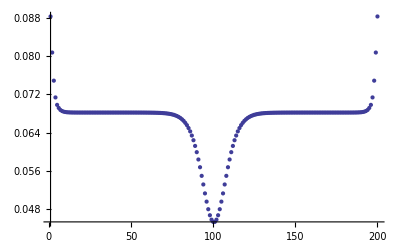

```mathematica
ListPlot[ϕ1,PlotRange->All]
```

```mathematica
{𝓉0,𝓉e,α,𝓀}={4.0,0.09,4.9,19.9};
```

```mathematica
Dim[𝓉0,𝓉e,α,𝓀,ϕ1,1000]
```

{38.82922,Null}

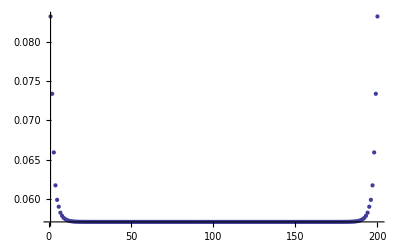

```mathematica
ListPlot[ϕ,PlotRange->All]
```

```mathematica
Export["dphi.dat",ϕ]
```

dphi.dat

```mathematica
ClearAll[Dim2,elecT,kineT,potT,chaT];
Dim2[𝓉0_,𝓉e_,α_,𝓀_,ϕ1_,time_]:=
(
{𝒩,𝒜,ℳ}=
{200,1.22,(931.4943 13)/9};
ϕ=ϕ1;
{elecT,kineT,potT,chaT,c,e}=Array[{}&,6];
𝓋=Array[0&,{𝒩}];
Φ={};
{ℯ,𝒸}={1,0};
(*hamiltonian*)
ls=-Array[𝓉0+α (-1)^(#+1) (ϕ[[#+1]]+ϕ[[#]])+(-1)^(#+1) 𝓉e&,199];
ls=Append[ls,0];
ls2=DiagonalMatrix[ls];
ℋ=RotateRight[ls2]+Transpose@RotateRight[ls2];

(*eigen problem*)
{ℰ,𝒵}=Transpose@Sort[Transpose[Eigensystem[ℋ]], #1[[1]] < #2[[1]] &];

For[t=1,t≤ time,t++,
(*start*)

(*hamiltonian*)
ls=-Array[𝓉0+α (-1)^(#+1) (ϕ[[#+1]]+ϕ[[#]])+(-1)^(#+1) 𝓉e&,199];
ls=Append[ls,0];
ls2=DiagonalMatrix[ls];
ℋ=RotateRight[ls2]+Transpose@RotateRight[ls2];

(*eigen problem*)
{ℰ,𝒵}=Transpose@Sort[Transpose[Eigensystem[ℋ]], #1[[1]] < #2[[1]] &];

(*bcd*)
𝓅=Array[2&,𝒩/2-1]~Join~{ℯ,𝒸};
{w1,w2,it}=
{Transpose[𝒵]⟦1;;199,1;;101⟧,Transpose[𝒵]⟦2;;200,1;;101⟧,
Array[𝓅&,199]};
r𝒲=Apply[Plus,w1 it w2,{1}];
𝒦=(Plus@@r𝒲)(2α)/200;

(*fh*)
ℱ=Insert[(Rest@r𝒲-Most@r𝒲)Riffle[Array[-1&,198/2],Array[1&,198/2]] 2 α-(ϕ⟦3;;200⟧+2ϕ⟦2;;199⟧+ϕ⟦1;;198⟧) 𝓀,0,{{1},{-1}}]+{2 α r𝒲⟦1⟧-𝓀(ϕ⟦1⟧+ϕ⟦2⟧)-𝒦}~Join~Array[0&,198,2]~Join~{2 α r𝒲⟦199⟧-𝓀(ϕ⟦199⟧+ϕ⟦200⟧)-𝒦};

(*classical motion*)
𝓋=0.98 𝓋+ℱ/ℳ;
ϕ=ϕ+𝓋 0.98;

ϕ[[2;;199]]=(ϕ[[1;;198]]+ϕ[[2;;199]]+ϕ[[3;;200]])/3;
Φ=Append[Φ,ϕ];

(*energy record*)
elect=ℯ ℰ[[99]]+𝒸 ℰ[[102]]+2 Plus@@ℰ[[1;;98]];
elecT=Append[elecT,elect];
kinet=𝓋.𝓋 ℳ/2;
kineT=Append[kineT,kinet];
dspl=Riffle[Array[1&,100],Array[-1&,100]]*ϕ;
Δdspl=dspl[[2;;]]-dspl[[1;;-2]];
pott=Δdspl.Δdspl*𝓀/2;
potT=Append[potT,pott];
chat=1.01 (elect+kinet+pott);
chaT=Append[chaT,chat];

]//AbsoluteTiming
)
```

```mathematica
Dim2[𝓉0,𝓉e,α,𝓀,ϕ,1000]
```

{36.34808,Null}

```mathematica
ListPlot[#1,PlotRange->All]&/@{elecT,kineT,potT,chaT}
```

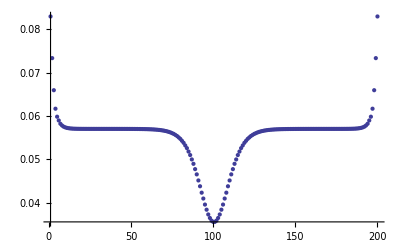

```mathematica
ListPlot[ϕ,PlotRange->All]
```

```mathematica
Export["adphi.dat",ϕ]
```

adphi.dat

```mathematica
Directory[]
```

```mathematica
SetDirectory@NotebookDirectory[]
```

```mathematica
Export["transport4.dat",ϕ]
```

```mathematica
SetDirectory@NotebookDirectory[]
```

D:\MMA_Scripts\Research\Theory

```mathematica
ϕ=Flatten@Import["transport.dat"];
```

```mathematica
ListPlot[ϕ,PlotRange->All]
```

-Graphics-

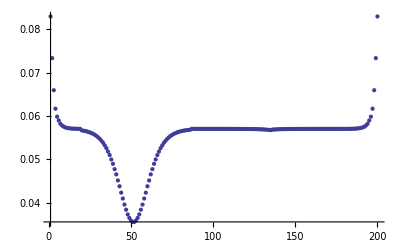

```mathematica
ld=RotateLeft[ϕ[[20;;135]],49];
ϕ[[20;;135]]=ld;
ListPlot[ϕ,PlotRange->All]
```

## Checking

```mathematica
ϕ[[50]]-ϕ[[100]]
```

```mathematica
{Position[ϕ,#1],#1}&/@Cases[ϕ,x_/;x-0.05<0.0001:>x]
```

```mathematica
ϕ[[93]]-ϕ[[108]]
```

```mathematica
Export["phi.dat",ϕ]
```

```mathematica
SystemOpen[DirectoryName[AbsoluteFileName["phi.dat"]]]
```

```mathematica
Remove[Dim]
```

## Transport

```mathematica
ClearAll[Formation,psy];
Formation[𝓉0_,𝓉e_,α_,𝓀_,ϕ1_,time_,intensity_,et_,tend_]:=
(
{𝒩,𝒯,ℐ0,𝒜,ℳ,𝔈}=
{200,1000,intensity,(*0.3 9.1 10^-5,*)1.22,(931.4943 13)/9,2*10^-4*et};
ϕ=ϕ1;
{elecT,kineT,potT,chaT,c,e,psy[0],psy[1],psy[2],psy[3]}=Array[{}&,10];
𝓋=Array[0&,{𝒩}];
Φ={};
{ℯ,𝒸}={1,0};
(*hamiltonian*)
ls=-Array[𝓉0+α (-1)^(#+1) (ϕ[[#+1]]+ϕ[[#]])+(-1)^(#+1) 𝓉e&,199];
ls=Append[ls,0];
ls2=DiagonalMatrix[ls];
lsE=DiagonalMatrix[Range[200] 𝔈 𝒜];
ℋ=RotateRight[ls2]+Transpose@RotateRight[ls2]+lsE;

(*eigen problem*)
{ℰ,𝒵}=Transpose@Sort[Transpose[Eigensystem[ℋ]], #1[[1]] < #2[[1]] &];

For[t=1,t≤ time,t++,
If[t≥tend,ℐ=ℐ0,ℐ=0];
(*start*)

(*hamiltonian*)
ls=-Array[𝓉0+α (-1)^(#+1) (ϕ[[#+1]]+ϕ[[#]])+(-1)^(#+1) 𝓉e&,199];
ls=Append[ls,0];
ls2=DiagonalMatrix[ls];
ℋ=RotateRight[ls2]+Transpose@RotateRight[ls2]+lsE;

(*eigen problem*)
{ℰ,𝒵}=Transpose@Sort[Transpose[Eigensystem[ℋ]], #1[[1]] < #2[[1]] &];
psy[0]=Append[psy[0],𝒵[[99]]^2];
psy[1]=Append[psy[1],𝒵[[100]]^2];
psy[2]=Append[psy[2],𝒵[[101]]^2];
psy[3]=Append[psy[3],𝒵[[102]]^2];
(*bcd*)
𝓅=Array[2&,𝒩/2-1]~Join~{ℯ,𝒸};
{w1,w2,it}=
{Transpose[𝒵]⟦1;;199,1;;101⟧,Transpose[𝒵]⟦2;;200,1;;101⟧,
Array[𝓅&,199]};
r𝒲=Apply[Plus,w1 it w2,{1}];
𝒦=(Plus@@r𝒲)(2α)/200;

(*fh*)
ℱ=Insert[(Rest@r𝒲-Most@r𝒲)Riffle[Array[-1&,198/2],Array[1&,198/2]] 2 α-(ϕ⟦3;;200⟧+2ϕ⟦2;;199⟧+ϕ⟦1;;198⟧) 𝓀,0,{{1},{-1}}]+{2 α r𝒲⟦1⟧-𝓀(ϕ⟦1⟧+ϕ⟦2⟧)-𝒦}~Join~Array[0&,198,2]~Join~{2 α r𝒲⟦199⟧-𝓀(ϕ⟦199⟧+ϕ⟦200⟧)-𝒦};

(*classical motion*)
𝓋=0.95 𝓋+ℱ/ℳ;
ϕ=ϕ+𝓋 0.95;

ϕ[[2;;199]]=(ϕ[[1;;198]]+ϕ[[2;;199]]+ϕ[[3;;200]])/3;
Φ=Append[Φ,ϕ];

(*transition dipole moment*)
rd=𝒜 Plus@@(𝒵[[101]] Array[#&,200] 𝒵[[100]]);

𝓇=(rd^2) 3.76 10^-3 (ℰ[[101]]-ℰ[[100]])^3;

(*population variation*)
𝒸=𝒸-𝓇 𝒸 10^-6+ℯ (rd^2) ℐ-𝒸 (rd^2) ℐ;
ℯ=1-𝒸;(*============2 or 1============*)

(*record c and e*)
c=Append[c,𝒸];
e=Append[e,ℯ];
]//AbsoluteTiming
)
```

```mathematica
{𝓉0,𝓉e,α,𝓀}={4.0,0.09,4.9,19.9};
```

```mathematica
ϕ2=ϕ;
```

```mathematica
Formation[𝓉0,𝓉e,α,𝓀,ϕ2,1000,.2 9.1 10^-5,3.,200]
```

{20.07415,Null}

```mathematica
ListDensityPlot[psy[1][[1;;1000;;10,All]],PlotRange->All,ColorFunction->ColorData["AvocadoColors"],DataRange->{{0,200},{1,1000}},ImageSize->380,FrameStyle->Directive[Thickness[0.006],FontSize->23,Bold],FrameLabel->{Style["Lattice Site",FontSize->23,Bold],Style["Time (fs)",FontSize->23,Bold]}]
```

```mathematica
p[1]=ListPlot3D[psy[1][[1;;1000;;10,All]],PlotRange->All,DataRange->{{0,200},{1,1000}},Mesh->10,ColorFunctionScaling->True,Lighting->Automatic,PlotStyle->Opacity[0.8],ColorFunction->Function[{x,y,z},ColorData[{"Rainbow","Reverse"}][Rescale[z,{0,0.9}]]]]
```

```mathematica
Show[p[1],BoxStyle->Directive[{Bold,FontSize->20,Thickness[0.006]}],ImageSize->450,Axes-> True,LabelStyle->Directive[Bold,20],PlotLabel->Style[" ",Bold,20],AspectRatio->1/1.218,Ticks->{Automatic,Array[#1&,5,{0,1000}],Automatic},ViewPoint->{-2.11899347072187,2.1819542421422633,-1.4828831229181403},ViewVertical->{0,0,-1},AxesLabel->{Nest[StringJoin[" ",#1]&,"Lattice Site",10],Nest[StringJoin[" ",#1]&,"Times (fs)   ",0],""}]
```

```mathematica
Export["fig_cweak.dat",c];
```

```mathematica
Export["fig_eweak.dat",e];
```

```mathematica
Export["fig2.dat",psy[1]];
Export["fig2_c.dat",c];
```

```mathematica
Export["fig3.dat",psy[1]];
Export["fig3_c.dat",c];
```

```mathematica
Export["fig4.dat",psy[1]];
Export["fig4_c.dat",c];
Export["config.dat",Φ[[1;;1000;;10]]];
```

```mathematica
Export["fig4.dat",psy[1]];
```

```mathematica
Export["configweak.dat",Φ[[1;;1000;;10]]];
```

```mathematica
p[1]=ListPlot3D[Φ[[1;;400;;1,All]],PlotRange->All,DataRange->{{0,200},{1,1000}}]
```

```mathematica
Options@-Graphics3D-
```

```mathematica
renderp[1]=Show[p[1],BoxStyle->Directive[{Bold,FontSize->20,Thickness[0.006]}],ImageSize->400,Axes-> True,LabelStyle->Directive[Bold,20],PlotLabel->Style["(a)",Bold,20],AspectRatio->1/1.218,Ticks->{Automatic,Array[#1&,5,{0,1000}],Automatic},ViewPoint->{-2.736869976070171,-1.1181962999758488,-1.6459586169785627},ViewVertical->{0,0,-1},AxesLabel->{Nest[StringJoin[" ",#1]&,"Lattice Site",20],Nest[StringJoin[" ",#1]&,"Times (fs)",4],""}]
```

```mathematica
Export["fig6.png",renderp[1],ImageResolution->600]
```

```mathematica
SystemOpen["fig6.png"]
```

```mathematica
rp1=ListDensityPlot[Φ[[1;;1000;;10,All]],PlotRange->All,ColorFunction->ColorData["TemperatureMap"],DataRange->{{0,200},{0,1000}},ImageSize->400,FrameStyle->Directive[Thickness[0.006],FontSize->20,Bold],FrameLabel->{Style["Lattice Site",FontSize->20,Bold],Style["Time (fs)",FontSize->20,Bold]}]
```

```mathematica
ListPlot[c,PlotRange->All]
```

## Fig2

```mathematica
ListDensityPlot[psy[[1;;1000;;10,All]],PlotRange->All,ColorFunction->ColorData["AvocadoColors"],DataRange->{{0,200},{1,1000}},ImageSize->380,FrameStyle->Directive[Thickness[0.006],FontSize->23,Bold],FrameLabel->{Style["Lattice Site",FontSize->23,Bold],Style["Time (fs)",FontSize->23,Bold]}]
```

```mathematica
fig[2]=ListDensityPlot[psy[[150;;400;;1,40;;150]],PlotRange->All,ColorFunction->ColorData["AvocadoColors"],DataRange->{{40,150},{150,400}},ImageSize->380,FrameStyle->Directive[Thickness[0.006],FontSize->23,Bold],FrameLabel->{Style["Lattice Site",FontSize->23,Bold],Style["Time (fs)",FontSize->23,Bold]}]
```

```mathematica
ListDensityPlot[ Φ[[200;;250;;1,40;;150]],PlotRange->All,ColorFunction->ColorData["AvocadoColors"],DataRange->{{40,150},{200,250}},ImageSize->380,FrameStyle->Directive[Thickness[0.006],FontSize->23,Bold],FrameLabel->{Style["Lattice Site",FontSize->23,Bold],Style["Time (fs)",FontSize->23,Bold]}]
```

```mathematica
Export["fig2.png",fig[2],ImageResolution->600]
```

```mathematica
SystemOpen["fig2.png"]
```

## Photon-dependent

{𝓉0, 𝓉e, α, 𝓀} = {4.0, 0.09, 5.0 - 0.1, 19.9};

```mathematica
ϕ=Flatten@Import["transport.dat"];
```

```mathematica
ListPlot[ϕ,PlotRange->All]
```

```mathematica
ld=RotateLeft[ϕ[[20;;135]],49];
ϕ[[20;;135]]=ld;
ListPlot[ϕ,PlotRange->All]
```

```mathematica
ϕ2=ϕ;
```

```mathematica
Array[(Formation[𝓉0,𝓉e,α,𝓀,ϕ2,1000,#1,3,200]//AbsoluteTiming;Export[ToString[N[#1]]<>"psy.dat",psy[[1;;1000;;10]]];Export[ToString[N[#1]]<>"phi.dat",Φ[[1;;1000;;10]]];)&,10,{1*9.1*10^(-5),100*9.1*10^(-5)}];
```

```mathematica
Directory[]
```

```mathematica
FileNames["*.dat"]
```

### plot

```mathematica
ClearAll["Global`*"];
```

```mathematica
sample=Import["0.002093phi.dat"];
```

```mathematica
Dimensions@sample
```

```mathematica
ListDensityPlot[sample[[1;;100,1;;200]],PlotRange->All,ColorFunction->ColorData["AvocadoColors"],DataRange->{{0,200},{1,1000}},ImageSize->380,FrameStyle->Directive[Thickness[0.006],FontSize->23,Bold],FrameLabel->{Style["Lattice Site",FontSize->23,Bold],Style["Time (fs)",FontSize->23,Bold]}]
```

```mathematica
ListPlot@sample[[1]]
```

```mathematica
line=Min[sample[[#1]]]&/@Range[100];
```

```mathematica
Position[sample[[20]],line[[20]]][[1,1]]
```

```mathematica
pos=Position[sample[[#1]],line[[#1]]][[1,1]]&/@Range[100];
```

```mathematica
sam=Transpose[{pos,10Range[100]}];
```

```mathematica
sam[[20]]
```

```mathematica
ListPlot[sam,Joined->True,PlotRange->{{0,200},Automatic}]
```

## fig2

```mathematica
ϕ=Flatten@Import["transport.dat"];
```

```mathematica
ld=RotateLeft[ϕ[[20;;135]],49];
ϕ[[20;;135]]=ld;
ListPlot[ϕ,PlotRange->All]
```

-Graphics-

```mathematica
ϕ2=ϕ;
```

```mathematica
Formation[𝓉0,𝓉e,α,𝓀,ϕ2,1000,0 9.1 10^-5,3,0]
```

{20.00114,Null}

```mathematica
ListDensityPlot[psy[[1;;600;;10,All]],PlotRange->All,ColorFunction->ColorData["AvocadoColors"],DataRange->{{0,200},{1,600}},ImageSize->380,FrameStyle->Directive[Thickness[0.006],FontSize->23,Bold],FrameLabel->{Style["Lattice Site",FontSize->23,Bold],Style["Time (fs)",FontSize->23,Bold]}]
```

Part::take: Cannot take positions 1 through 600 in psy.

ListDensityPlot::arrayerr: psy ⟦ 1 ;; 600 ;; 10, All ⟧ must be a valid array.

ListDensityPlot[psy⟦1;;600;;10,All⟧,PlotRange→All,ColorFunction→ColorDataFunction[{0,1},-Graphics-],DataRange→{{0,200},{1,600}},ImageSize→380,FrameStyle→Directive[Thickness[0.006],FontSize→23,Bold],FrameLabel→{Lattice Site,Time (fs)}]

```mathematica
Export["fig2.dat",psy[[1;;600;;10,All]]]
```

```mathematica
ListPlot[c,PlotRange->{{0,1000},{-.02,.2}},Axes->False,Frame->True,FrameStyle->Directive[Thickness[0.006],FontSize->23,Bold],FrameLabel->{Style["Time (fs)",FontSize->23,Bold],Style["Electro Population",FontSize->23,Bold]},ImageSize->400]
```

```mathematica
Export["fig2_c.dat",c]
```

```mathematica
Export["fig2_e.dat",e]
```

fig2_e.dat

## f3

```mathematica
ϕ=Flatten@Import["transport.dat"];
```

```mathematica
ld=RotateLeft[ϕ[[20;;135]],49];
ϕ[[20;;135]]=ld;
ListPlot[ϕ,PlotRange->All]
```

```mathematica
ϕ2=ϕ;
```

```mathematica
Formation[𝓉0,𝓉e,α,𝓀,ϕ2,1000,20 9.1 10^-5,0,0]
```

{20.21016,Null}

```mathematica
ListDensityPlot[psy[[1;;600;;10,All]],PlotRange->All,ColorFunction->ColorData["AvocadoColors"],DataRange->{{0,200},{1,600}},ImageSize->380,FrameStyle->Directive[Thickness[0.006],FontSize->23,Bold],FrameLabel->{Style["Lattice Site",FontSize->23,Bold],Style["Time (fs)",FontSize->23,Bold]}]
```

```mathematica
Export["fig3.dat",psy[[1;;600;;10,All]]]
```

```mathematica
ListPlot[c,PlotRange->{{0,400},{-.02,.6}},Axes->False,Frame->True,FrameStyle->Directive[Thickness[0.006],FontSize->23,Bold],FrameLabel->{Style["Time (fs)",FontSize->23,Bold],Style["Electro Population",FontSize->23,Bold]},ImageSize->400]
```

```mathematica
Export["fig3_c.dat",c]
```

```mathematica
Export["fig3_e.dat",e]
```

fig3_e.dat

## fig 4

```mathematica
ϕ=Flatten@Import["transport.dat"];
```

```mathematica
ld=RotateLeft[ϕ[[20;;135]],49];
ϕ[[20;;135]]=ld;
ListPlot[ϕ,PlotRange->All]
```

```mathematica
ϕ2=ϕ;
```

```mathematica
Formation[𝓉0,𝓉e,α,𝓀,ϕ2,1000,20 9.1 10^-5,3,200]
```

```mathematica
Dimensions@psy
```

```mathematica
ListDensityPlot[psy[[1;;800;;10,All]],PlotRange->All,ColorFunction->ColorData["AvocadoColors"],DataRange->{{0,200},{1,800}},ImageSize->380,FrameStyle->Directive[Thickness[0.006],FontSize->23,Bold],FrameLabel->{Style["Lattice Site",FontSize->23,Bold],Style["Time (fs)",FontSize->23,Bold]}]
```

```mathematica
Export["fig4.dat",psy[[1;;800;;10,All]]]
```

```mathematica
ListPlot[c,PlotRange->{{0,800},{-.01,.1}},Axes->False,Frame->True,FrameStyle->Directive[Thickness[0.006],FontSize->23,Bold],FrameLabel->{Style["Time (fs)",FontSize->23,Bold],Style["Electro Population",FontSize->23,Bold]},ImageSize->400]
```

```mathematica
Export["fig4_c.dat",c]
```